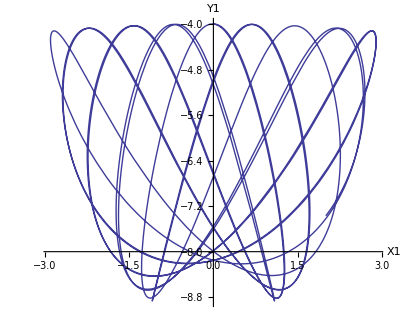

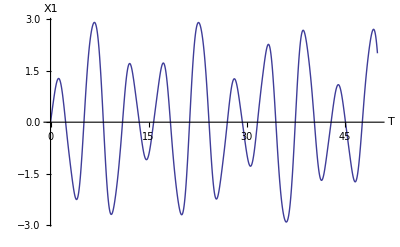

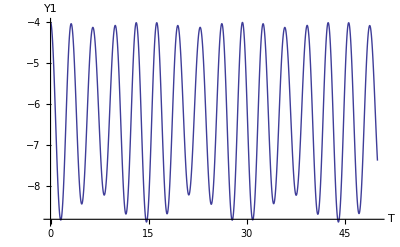

```mathematica
Clear["Global`*"]
g=9.8;m=1;k=4;
L0=4;tm=50;v0=1.4;
initial1={0,v0};
initial2={-L0,0};
equs=
{x1''[t]==-x1[t]*(1-L0/(√((x1[t])^2+(y1[t])^2)))*k/m,
y1''[t]== -y1[t]*(1-L0/(√((x1[t])^2+(y1[t])^2)))*k/m-g,
x1'[0]==initial1[[2]],x1[0]== initial1[[1]],
y1'[0]==initial2[[2]],y1[0]==initial2[[1]]};
s=NDSolve[equs,{x1,y1},{t,0,tm},Method->"ExplicitRungeKutta" ];
{x1,y1}={x1,y1}/.s[[1]];
ParametricPlot[{x1[t],y1[t]},{t,0,tm},AxesLabel->{"X1","Y1"}]
Plot[x1[t],{t,0,50},AxesLabel->{"T","X1"}]
Plot[y1[t],{t,0,50},AxesLabel->{"T","Y1"}]
Clear[g,equs,s,x1,y1,initial1,initial2]
```